```mathematica
Dynamic[{n,c,ds,Norm@f[xI,parsI,TR1+dT ds,uR1]}]
```

```mathematica
Norm@f[uR1,pars0,TR1,e8m1br01]
```

1.46468×10^-10

```mathematica
Graphics3D[{{Red,PointSize@Medium,Point[Partition[u1[[;;180]],3]]},{Blue,PointSize@Medium,Point[Partition[u0,3]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxD,{2}]]}},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[xI,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[xI,pars0,T1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[xI,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[u1,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[uR1,pars0,TR1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[uR1,pars0,TR1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[uR1,pars0,TR1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
StringReplace[ToString@e8m1br01[[-1,1]],"."->""]
```

0512636

```mathematica
animation=Table[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[e8m1br01[[-1,2]],pars0,e8m1br01[[-1,1]]][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[e8m1br01[[-1,2]],pars0,e8m1br01[[-1,1]]][t],3][[;;60]][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[e8m1br01[[-1,2]],pars0,e8m1br01[[-1,1]]][t],3][[;;60]][[#]]&,idxD,{2}]]}},PlotRange->4,ImageSize->Large,Boxed->False],{t,0,1,1/50}];
```

```mathematica
Export[NotebookDirectory[]<>"E"<>ToString@l<>"-1-"<>StringReplace[ToString@e8m1br01[[-1,1]],"."->""]<>".gif",animation,"DisplayDurations"->1/25,"AnimationRepetitions"->∞]
```

$Failed

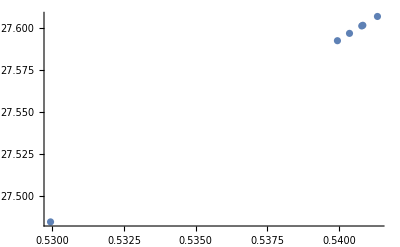

```mathematica
ListPlot[{#1,Norm@#2}&@@@e8m1br01]
```